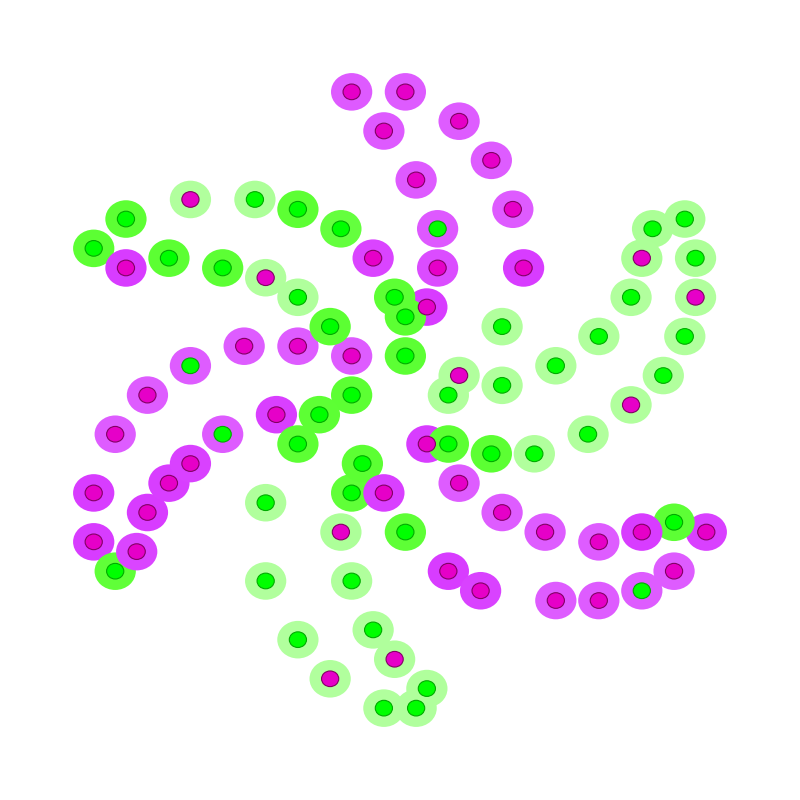

```mathematica
ClearAll["Global`*"]

initializePinWheelData[] := (

pinWheelXYhat = { { -4 , 4 , 1 } , { -9 , 5 , 1 } , { -14 , 5 , 1 } , { -19 , 3 , 0 } , { -23 , 0 , 1 } , { -26 , -4 , 1 } , { -28 , -10 , 1 } , { -28 , -15 , 1 } , { -26 , -18 , 0 } , { -24 , -16 , 1 } , { -23 , -12 , 1 } , { -21 , -9 , 1 } , { -19 , -7 , 1 } , { -16 , -4 , 0 } , { -11 , -2 , 1 } , { -4 , 0 , 0 } , { -7 , -2 , 0 } , { -9 , -5, 0 } , { -12 , -11 , 0 } , { -12 , -19 , 0 } , { -9 , -25 , 0 } , { -6 , -29 , 1 } , { -1 , -32 , 0 } , {  2 , -32 , 0 } , {  3 , -30 , 0 } , {  0 , -27 , 1 } , { -2 , -24 , 0 } , { -4 , -19 , 0 } , { -5 , -14 , 1 } , { -4 , -10 , 0 } , { -3 , -7 , 0 } , { -1 , -10 , 1 } , {  1 , -14 , 0 } , {  5 , -18 , 1 } , {  8 , -20 , 1 } , {  15 , -21 , 1 } , {  19 , -21 , 1 } , {  23 , -20 , 0 } , {  26 , -18 , 1 } , {  29 , -14 , 1 } , {  26 , -13 , 0 } , {  23 , -14 , 1 } , {  19 , -15 , 1 } , {  14 , -14 , 1 } , {  10 , -12 , 1 } , {  6 , -9 , 1 } , {  3 , -5 , 1 } , {  5 , -5 , 0 } , {  9 , -6 , 0 } , {  13 , -6 , 0 } , {  18 , -4 , 0 } , {  22 , -1 , 1 } , {  25 , 2 , 0 } , {  27 , 6 , 0 } , {  28 , 10 , 1 } , {  28 , 14 , 0 } , {  27 , 18 , 0 } , {  24 , 17 , 0 } , {  23, 14 , 1 } , {  22 , 10 , 0 } , {  19 , 6 , 0 } , {  15 , 3 , 0 } , {  10 , 1 , 0 } , {  5 , 0 , 0 } , {  6 , 2 , 1 } , {  10 , 7 , 0 } , {  12 , 13 , 1 } , {  11 , 19 , 1 } , {  9 , 24 , 1 } , {  6 , 28 , 1 } , {  1 , 31 , 1 } , { -4 , 31 , 1 } , { -1 , 27 , 1 } , {  2 , 22 , 1 } , {  4 , 17 , 0 } , {  4 , 13 , 1 } , { 3 , 9 , 1 } , { 1 , 4 , 0 } , { 1 , 8 , 0 } , { 0 , 10 , 0 } , {-2 , 14 , 1 } , {-5 , 17 , 0 } , {-9 , 19 , 0 } , {-13 , 20 , 0 } , {-19 , 20 , 1 } , {-25 , 18 , 0 } , {-28 , 15 , 0 } , {-25 , 13 , 1 } , {-21 , 14 , 0 } , {-16 , 13 , 0 } , {-12 , 12 , 1 } , {-9 , 10 , 0 } , {-6 , 7 , 0 } } ;
jCost = Table[ 0 , 93 ] ;
myX := {} ;
myY := {} ;

(* Initialize visualization *)

purpleXY := {} ;
greenXY := {} ;
guessHalo := {} ;

radius := 0.8 ;

For[ t=1 , t ≤ Length[ pinWheelXYhat ] , t++ ,
thisDataPoint := Flatten[ pinWheelXYhat[[ t ]] ] ;
If[ thisDataPoint[[ 3 ]] == 1 ,
AppendTo[ purpleXY , { { thisDataPoint[[1]] , thisDataPoint[[2]] } , radius } ] ,
AppendTo[ greenXY , { { thisDataPoint[[1]] , thisDataPoint[[2]] } , radius } ] 
] ;
AppendTo[ guessHalo , { { thisDataPoint[[1]] , thisDataPoint[[2]] } , radius * 2.4 } ] ;
] ;

(* load and normalize data *)
For[ ttt=1 , ttt ≤ Length[ pinWheelXYhat ] , ttt++ ,
(
thisDataPoint := Flatten[ pinWheelXYhat[[ ttt ]] ] ;
AppendTo[ myX , { thisDataPoint[[1]] / 36.0 , thisDataPoint[[2]] / 36.0 } ] ;
AppendTo[ myY , thisDataPoint[[ 3 ]] ] ;
)
] 

);

(*  ========================================================================== *)


learnByNetTrain[] := (

inp=Table[{pinWheelXYhat[[i,1]],pinWheelXYhat[[i,2]]}->pinWheelXYhat[[i,3]],{i,1,Length@pinWheelXYhat}] ;

(* net=NetChain[{LinearLayer[],LogisticSigmoid }]; *)

net=NetChain[{
LinearLayer[8] ,LogisticSigmoid ,
LinearLayer[10] ,LogisticSigmoid ,
LinearLayer[10] ,LogisticSigmoid ,
LinearLayer[10] ,LogisticSigmoid ,
LinearLayer[1] ,LogisticSigmoid  }] ;

trained=NetTrain[net,inp ] ;

localCurrentGuess = {} ;
For[ee= 1 , ee ≤ Length[ pinWheelXYhat ] , ee++ ,
thisXYanswer = Part[ pinWheelXYhat , ee ] ;
thisXY = { Part[ thisXYanswer , 1 ] , Part[ thisXYanswer , 2 ] } ;
AppendTo[ localCurrentGuess , trained[ thisXY ] ] ; 
] ;

Return[ localCurrentGuess ] ;

) ;

learnByLogisticRegression[] := ( 

(* initialize lists *)
w = { 0.01 , 0.01 } ;
b= { 0.00 };
dw = { 0.0 , 0.0 } ;
db= { 0.00 } ;
alpha = 0.03 ;

For[ yyy=1 , yyy≤256, yyy++ ,

(
(* do forward pass *)
z = myX.w ;

For[ qq=1 , qq<Length[ z ] , qq++ ,
z[[ qq ]] = z[[ qq ]] + b[[1]] ;
] ;
a = 1.0 / ( 1.0 + Exp[ - z ] ) ;

(* figure the cost *)
loss = - ( ( myY * Log[ a ] ) + ( 1 - myY ) * Log[ 1 - a ] ) ;
jCost = Total[ loss ] / Length[ loss ] ;

(* compute backprop values *)
dz = a - myY ;
dw = ( dz.myX ) / Length[ dz ] ;
db = Total[ dz ] / Length[ dz ] ;

(* update the weights *)
w = w - alpha * dw ;
b = b - alpha * db ;

)
] ;

Return[ a ] ;

) ;


computeHueSat[ localTrainedGuesses_ ] := (  
scaleFactor := 0.8 / ( Max[ Max[ localTrainedGuesses ] - 0.50 , 0.50  - Min[ localTrainedGuesses ] ] ) ;  
guessHues := {} ; 
guessSaturations := {} ;
For[ ss=1 , ss ≤ Length[ localTrainedGuesses ] , ss++ ,
thisGuess = localTrainedGuesses[[ ss ]]  ;
If[ thisGuess< 0.50 , ( AppendTo[ guessHues ,  0.3 ] ; AppendTo[ guessSaturations , scaleFactor * ( 0.50 - thisGuess ) ] ) ] ;
If[ thisGuess > 0.50 , (  AppendTo[ guessHues ,  0.8  ] ;  AppendTo[ guessSaturations , scaleFactor * ( thisGuess - 0.50 ) ] ) ] ;
If[ thisGuess == 0.50 ,  AppendTo[ guessHues ,  40  ] ] ;
] ;

combinedHueSatList = { guessHues , guessSaturations } ;
Return[ combinedHueSatList ] ;

) ;

(*  ==================================================================*)

doLearn[ trainSwitch_] := (

initializePinWheelData[] ;

If[ trainSwitch == 0 ,
trainedGuesses = learnByLogisticRegression[] ,
trainedGuesses= learnByNetTrain[] ;
] ;

hueSatLists := computeHueSat[ trainedGuesses ] ;
guessHues = Part[ hueSatLists , 1 ] ;
guessSaturations = Part[ hueSatLists , 2] ;

haloHues = {} ;
Clear@haloHues
haloHues=Array[sd,Length@guessHues];
Do[
haloHues[[i]]={guessHues[[i]],guessSaturations[[i]],1},
{i,1,Length@guessHues}
];

Graphics[ {

EdgeForm[],Transpose[{Hue/@haloHues ,Disk @@@ guessHalo}] ,
EdgeForm[{RGBColor[ 130/ 255 , 0 , 100 / 255 ] , Thick}], FaceForm[ RGBColor[ 230/ 255 , 0 , 200 / 255 ] ], Disk @@@ purpleXY  , 
EdgeForm[{Darker[ Green ] , Thick}], FaceForm[Green ], Disk @@@ greenXY 

} , ImageSize-> { 800 , 800 }
]

) 

(* doLearn[0] for logistic regression *)
(* doLearn[1] for NetTrain *)
 doLearn[1]
```